## Phases and Coefficiets

Prepare

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
ClearAll[n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList,k1A,k2A,a1A,a2A,range,range2];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

Parameters

```mathematica
thetamV=Pi/5;
k1V=0.3;
k2V=0.7;
a1V=0.1(*0.1(k1V)^(-5/3);*);
a2V=0.1(*0.1(k2V)^(-5/3)*);
phi1V=0;
phi2V=0;
```

```mathematica
distanceFun[n1_,n2_,k1Point_,k2Point_]:=Abs[n1*k1Point+n2*k2Point-1]/(√(n1^2+n2^2));
```

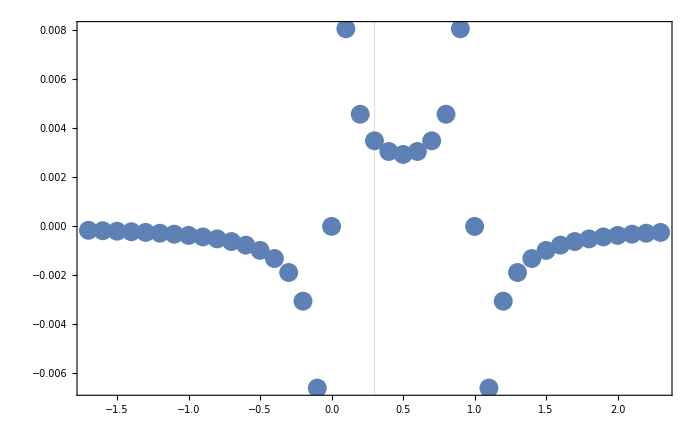

```mathematica
ListPlot[Table[{k1V+x,width2Freq[1,1,k1V+x,a1V,a2V,thetamV]},{x,-2,2,0.1}],PlotRange->Full,GridLines->{{k1V},None},ImageSize->imgsize,Frame->True]
```

```mathematica
fractionDis2Width[n1_,n2_,a1_,a2_,k1_,k2_,thetam_]:=distanceFun[n1,n2,k1,k2]/width2Freq[n1,n2,k1,a1,a2,thetam]
```

Coefficients

Test result for some example data.

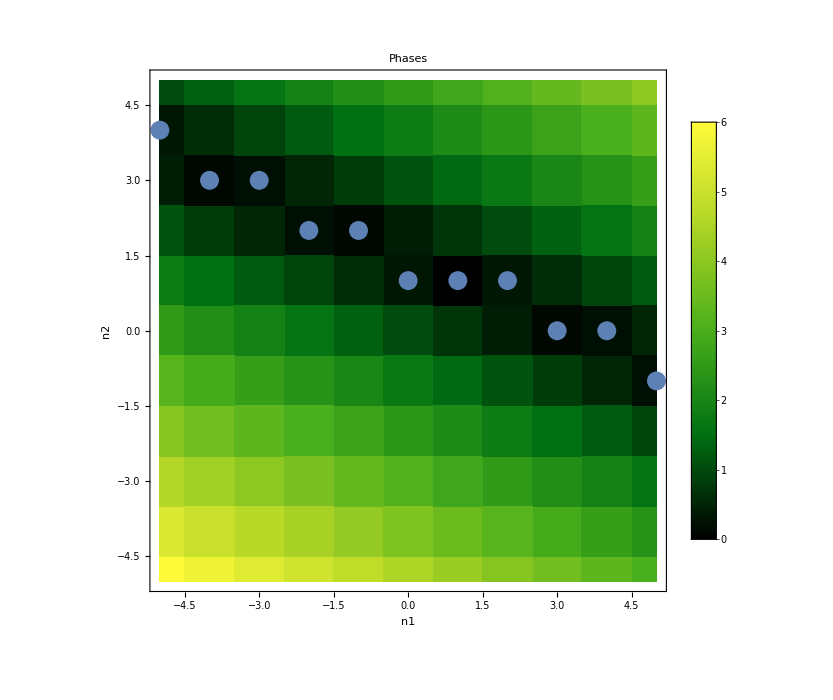
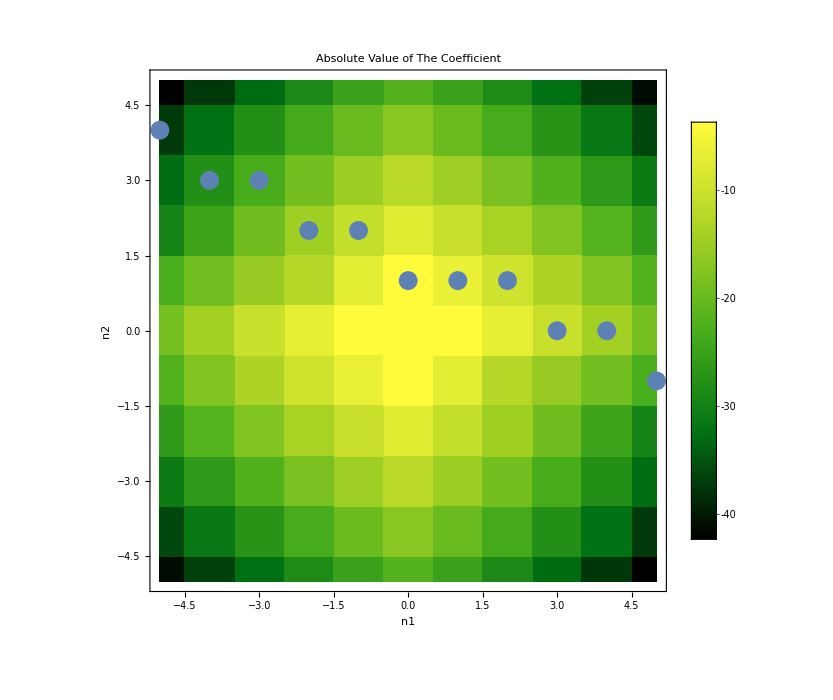
-Graphics- | -Graphics-
-Graphics- | -Graphics-
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2,order,endpoint},
k1A=k1V;
k2A=k2V;
a1A=a1V;(*0.1(k1A)^(-5/3);*)
a2A=a2V;(*(k2A)^(-5/3);*)
thetamA=thetamV;
range=5;
range2=5;
order=5;
endpoint=800;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
},{
Table[Show[pltN[k1A,k2A,a1A,a2A,thetamA,endpoint,Red],plt0Orders[k1A,k2A,a1A,a2A,thetamA,endpoint,ord,0,ToString[ord]<>",0;",Black](*,pltAll[k1,k2,a1,a2,order,Magenta]*),PlotRange->All],{ord,0,order}]
}
}]
]
(*Export["export/stimulated-2-freq-coef-non-approx-a2-larger-non-mesh.png",%]*)
```

## Compare with Previous calculations

We had a case where adding 1 and 2 will change the result but adding 3 doesn’t. They match the exact data when 4th order is added.

### First Case

k1=0.3;
k2=0.99;
a1=0.2*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

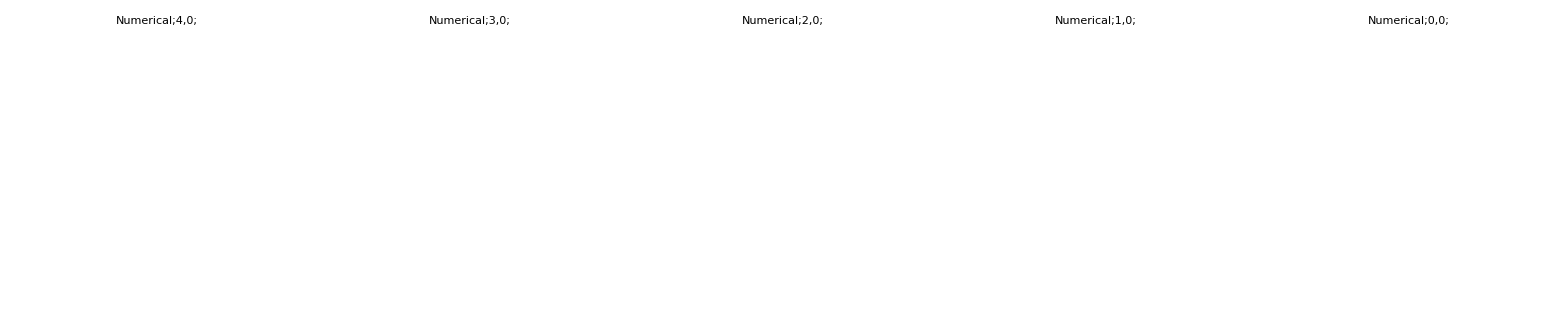

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.2*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

$Aborted

### Second Case

k1=0.3;
k2=0.99;
a1=0.4*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);

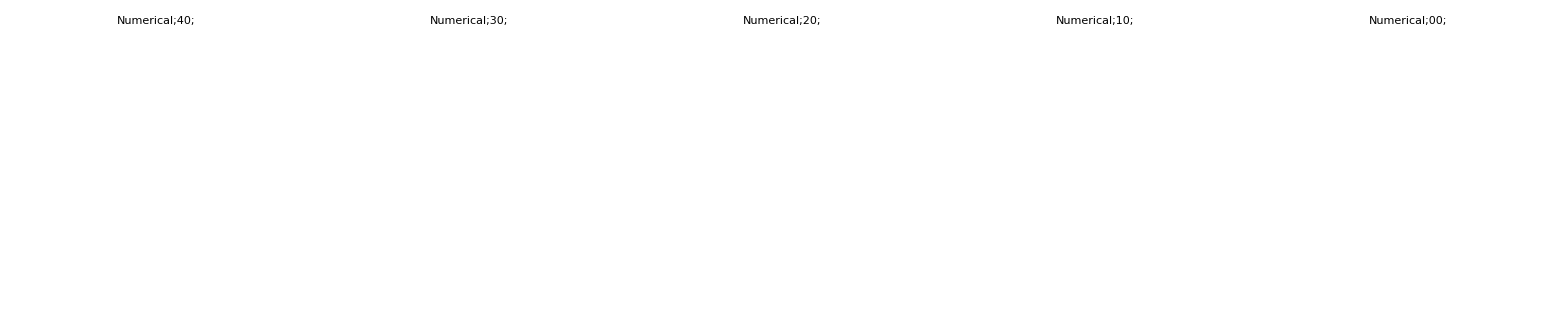

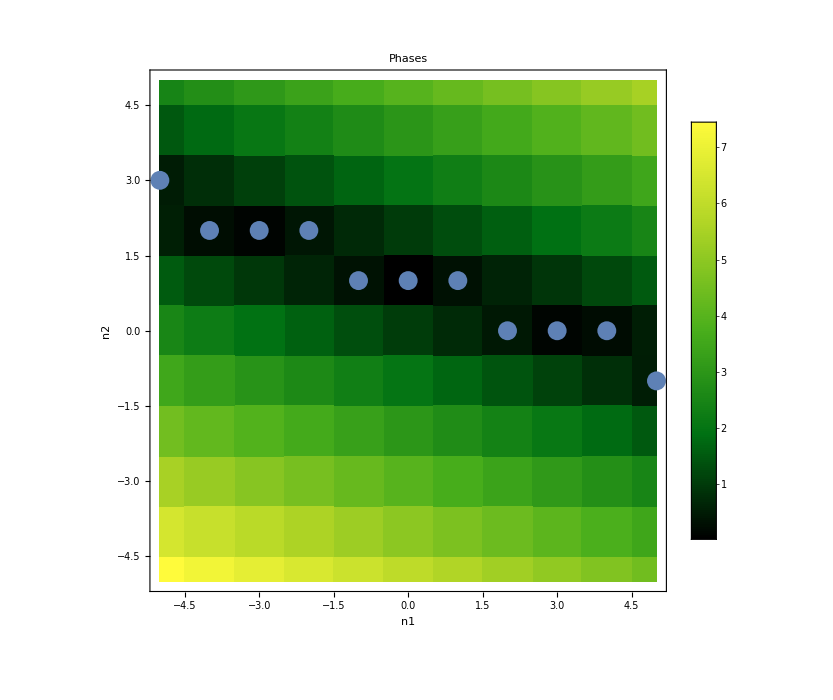
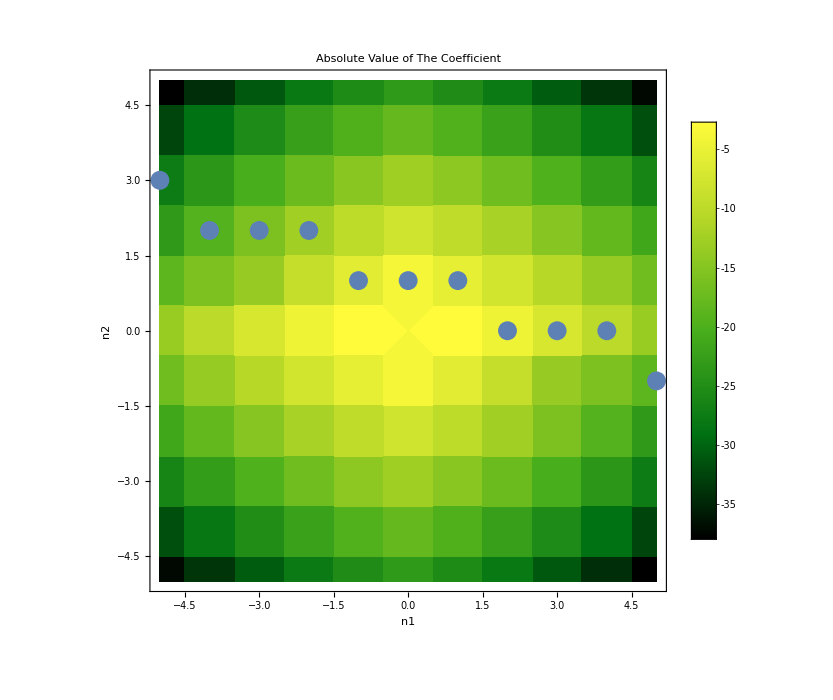
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Module[{k1A,k2A,a1A,a2A,thetamA,range,range2},
k1A=0.3;
k2A=0.99;
a1A=0.4*0.1(k1A)^(-5/3);
a2A=0.1(k2A)^(-5/3);
thetamA=thetamV;
range=5;
range2=5 ;
Grid[{{
coefDenPlt[k1A,k2A,a1A,a2A,thetamA,range]
},{
coefSlicings[k1A,k2A,a1A,a2A,thetamA,range,range2]
}}]
]
```

Resonances

```mathematica
amp2Freq[1.4,1,k1V,k2V,a1V,a2V,thetamV]
```

0.0000642386

```mathematica
n2Fun[n1_,k1_,k2_]:=Round[(1-n1*k1)/k2];
```

```mathematica
Table[{n1Table,n2Fun[n1Table,k1V,k2V]},{n1Table,-3,3}]
```

{{-3,3},{-2,2},{-1,2},{0,1},{1,1},{2,1},{3,0}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ √5 + 2\ √5\ ComplexInfinity encountered.

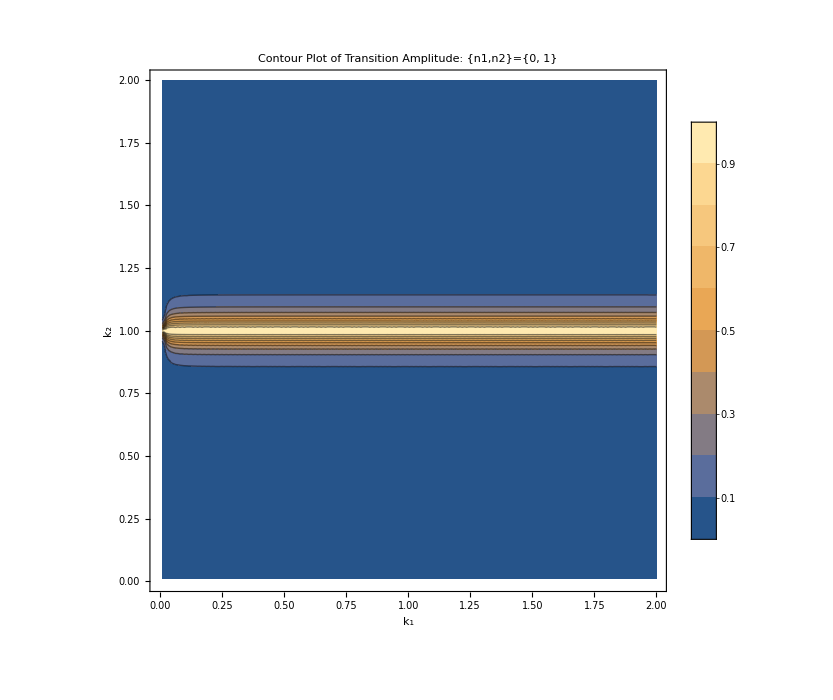
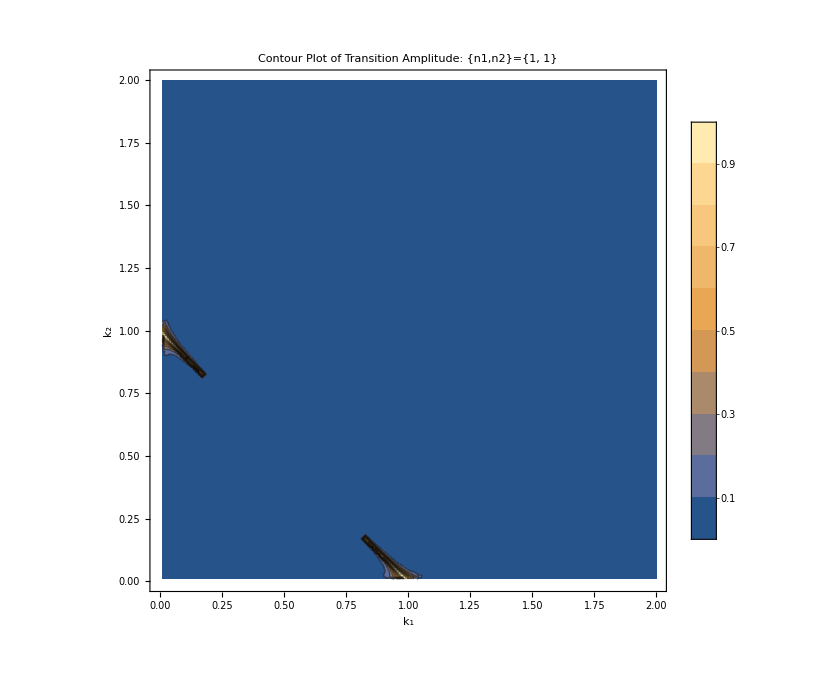
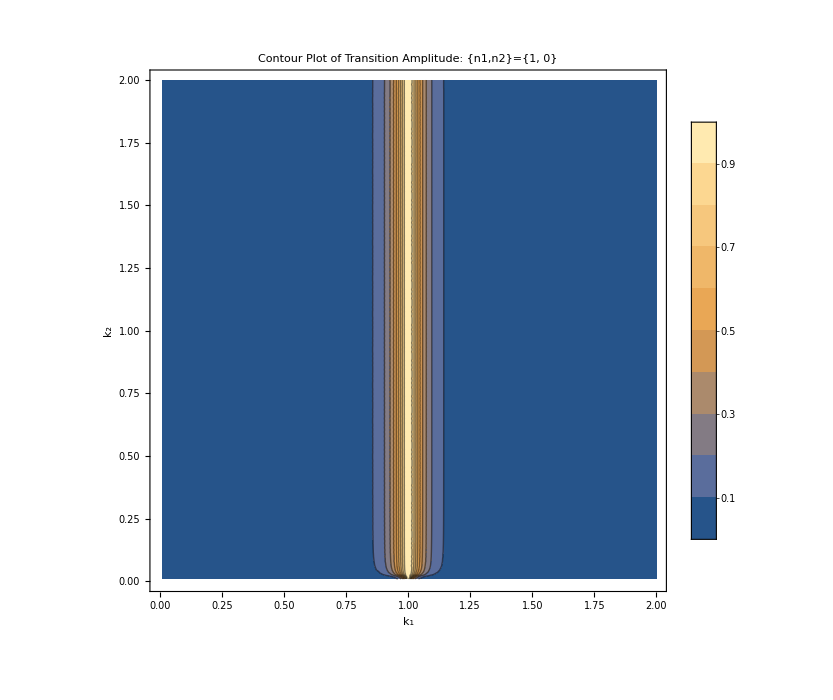
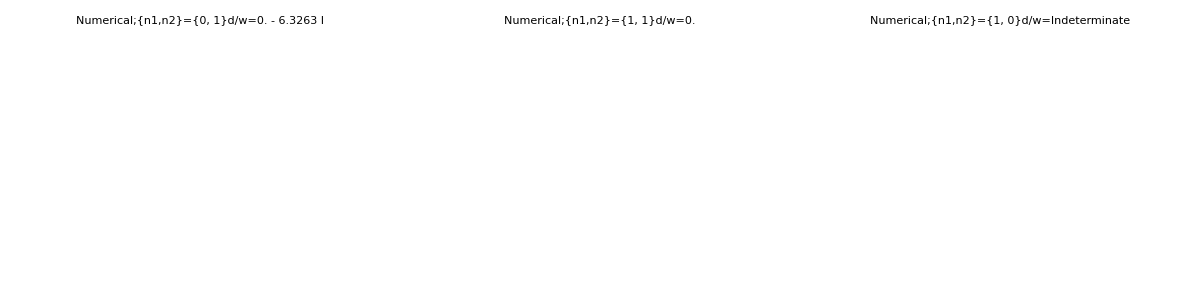
-Graphics- | -Graphics- | -Graphics-
-Graphics-

```mathematica
Module[{k1M,k2M,a1M,a2M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
thetamM=thetamV;
endpointM=1600;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-0,1},{n2M,-1,1}],1];*)

(*listOfn1n2=Table[{n1Table,n2Fun[n1Table,k1M,k2M]},{n1Table,-3,3}];*)
listOfn1n2={{0,1},{1,1},{1,0}};

Grid[{{
amp2FreqContourPltList[listOfn1n2,k1V,k2V,a1V,a2V,thetamV,{0.01,2},{0.01,2}]
},{
Grid[{Table[Show[pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2Table]<>"d/w="<>ToString[fractionDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],a1M,a2M,k1M,k2M,thetamM]],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
}}]

]
```

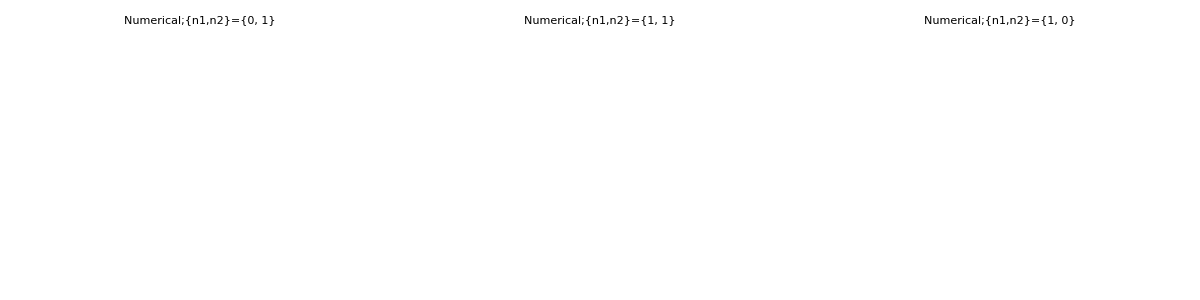
-Graphics-
-Graphics-

```mathematica
Module[{k1M,k2M,a1M,a2M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
thetamM=thetamV;
endpointM=1600;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-0,1},{n2M,-1,1}],1];*)
listOfn1n2={{0,1},{1,1},{1,0}};

Grid[{
{
Grid[{Table[Show[pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2Table],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
},{
Show[pltN[k1M,k2M,a1M,a2M,thetamM,endpointM,Red],plt0n1n2List[listOfn1n2,k1M,k2M,a1M,a2M,thetamM,endpointM,"",Blue],PlotRange->All]
}}]

]
```

```mathematica
Limit[hamiltonian0[1,1,0.95,k2Limit,0.1,0,π/5],k2Limit->0]
```

0.

```mathematica
Manipulate[amp2FreqPlt[n1x,n2x,a1V,a2V,thetamV,{0.5,0.7},{0.0001,0.2}],{{n1x,1,"n1"},-10,10,1,Appearance->"Labeled"},{{n2x,1,"n2"},-10,10,1,Appearance->"Labeled"}]
```

```mathematica
kRangeV={0.01,2,0.01};
nRangeV={-1,1};
nRange2V={-2,2};
n1n2ListV= {{0,1},{1,1},{1,0}};
```

-Graphics-

-Graphics-

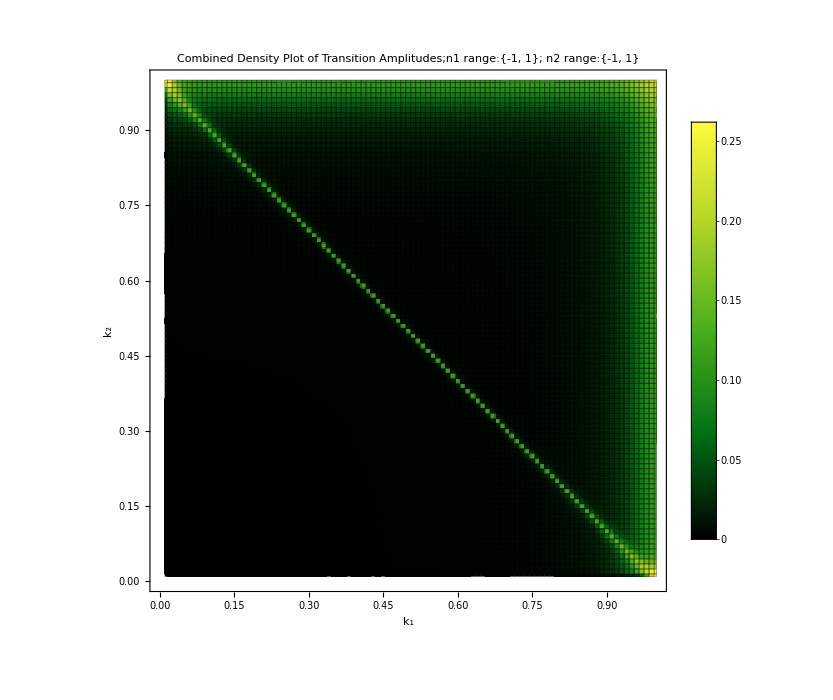

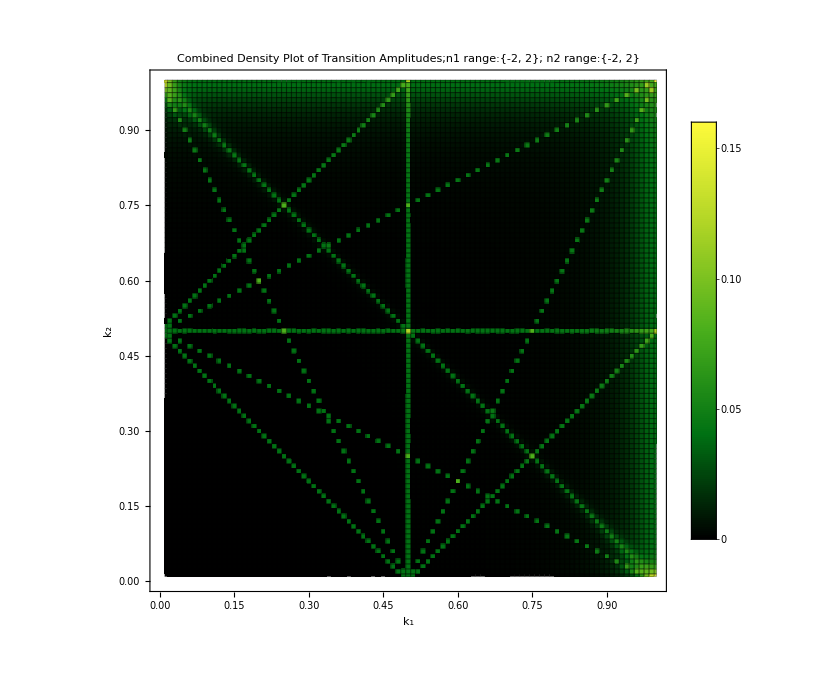

```mathematica
amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRangeV,nRangeV]
amp2FreqCombinedPlt[a1V,a2V,thetamV,kRangeV,kRangeV,nRange2V,nRange2V]
```

```mathematica
amp2FreqCombinedPlt2[a1V,a2V,thetamV,kRangeV,kRangeV,n1n2ListV]
```

-Graphics-